```mathematica
Clear[w,wo,wzx,wzy]
w=1;
wo=1;
wzx [nx_,nz_]:= wo √(1-(nz-nx)/wo);
wzy[ny_,nz_]:=1-(nz-ny)/wo;
Clear[ϵ1mn,ϵ1pn,ϵ2mn,ϵ2pn]
ϵ1mn[nx_,nz_,q_]:= √(1/2*((w^2+wzx[nx,nz]^2)-√((wzx[nx,nz]^2-w^2)^2+4*w^2*wzx[nx,nz]^2*q^2)));
ϵ1pn[nx_,nz_,q_]:= √(1/2*((w^2+wzx[nx,nz]^2)+√((wzx[nx,nz]^2-w^2)^2+4*w^2*wzx[nx,nz]^2*q^2)));
ϵ2mn[nx_,ny_,nz_,q_,ξ_]:= √(1/2*((1+wzy[ny,nz])-√((wzy[ny,nz]-1)^2+4*(1-ξ)^2/(1+ξ)^2*q^2*wzx[nx,nz]^2/wo^2)));
ϵ2pn[nx_,ny_,nz_,q_,ξ_]:= √(1/2*((1+wzy[ny,nz])+√((wzy[ny,nz]-1)^2+4*(1-ξ)^2/(1+ξ)^2*q^2*wzx[nx,nz]^2/wo^2)));
(*NORMAL vibrational modes*)

Clear[ϵ1mϵ2mn,ϵ1pϵ2pn]
ϵ1mϵ2mn[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1mn[nx,nz,q]*ϵ2mn[nx,ny,nz,q,ξ]];
ϵ1pϵ2pn[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1pn[nx,nz,q]*ϵ2pn[nx,ny,nz,q,ξ]];

(*Superradiant Phase*)
Clear[μx,wa,wb,wc,wd]
μx[nx_,nz_,q_] := 1/(wzx[nx,nz]^2/wo^2*(q^2-1)+1);
wa[nx_,nz_,q_]:=1/2*((wo/μx[nx,nz,q]-nz)*(1+μx[nx,nz,q])+nx*(1-μx[nx,nz,q]));
wb[nx_,nz_,q_]:=(1-μx[nx,nz,q])/8*(wo/(1+μx[nx,nz,q])*(3+μx[nx,nz,q])/μx[nx,nz,q]+nz+nx*((3*μx[nx,nz,q]^2-2*μx[nx,nz,q]+3)/(1-μx[nx,nz,q]^2)));
wc[nx_,ny_,nz_,q_]:=-1/8*ny*(1+μx[nx,nz,q]);
wd[nx_,nz_,q_]:=-(√2)/4*q*√(w/wo)*wzx[nx,nz]*(1-μx[nx,nz,q])/(√(1+μx[nx,nz,q]));
(*Mix Frequencies*)
Clear[w1,w2,w3]
w1[nx_,nz_,q_]:=wa[nx,nz,q]^2*(1+4*wb[nx,nz,q]/wa[nx,nz,q]);
w2[nx_,nz_,q_]:=√(w*wa[nx,nz,q])*(4*wd[nx,nz,q]+√2*q*√(w/wo)*wzx[nx,nz]*√(1+μx[nx,nz,q]));
w3[nx_,ny_,nz_,q_]:=1-4*wc[nx,ny,nz,q]/wa[nx,nz,q];
w4[nx_,nz_,q_,ξ_]:=(√2)/(√(wo*wa[nx,nz,q]))*wzx[nx,nz]*q*√(1+μx[nx,nz,q])*(1-ξ)/(1+ξ);
(*SUPERRADIANT vibrational modes*)
Clear[ϵ1ms,ϵ1ps,ϵ2ms,ϵ2ps,ϵ1mϵ2ms,ϵ1pϵ2ps]
ϵ1ms[nx_,ny_,nz_,q_]:=√(1/2*((w^2+w1[nx,nz,q]^2)-√((w^2-w1[nx,nz,q]^2)^2+w2[nx,nz,q]^2)));
ϵ1ps[nx_,ny_,nz_,q_]:=√(1/2*((w^2+w1[nx,nz,q]^2)+√((w^2-w1[nx,nz,q]^2)^2+w2[nx,nz,q]^2)));


ϵ2ms[nx_,ny_,nz_,q_,ξ_]:=√(1/2*((1+w3[nx,ny,nz,q])-√((w3[nx,ny,nz,q]-1)^2+w4[nx,nz,q,ξ]^2)));
ϵ2ps[nx_,ny_,nz_,q_,ξ_]:=√(1/2*((1+w3[nx,ny,nz,q])+√((w3[nx,ny,nz,q]-1)^2+w4[nx,nz,q,ξ]^2)));


ϵ1mϵ2ms[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1ms[nx,ny,nz,q]*ϵ2ms[nx,ny,nz,q,ξ]];
ϵ1pϵ2ps[nx_,ny_,nz_,q_,ξ_]:=Re[ϵ1ps[nx,ny,nz,q]*ϵ2ps[nx,ny,nz,q,ξ]];
```

```mathematica
Clear[mode]
mode[nx_,ny_,nz_,ξ_]:=Plot[{ϵ1mϵ2mn[nx,ny,nz,q,ξ],ϵ1pϵ2pn[nx,ny,nz,q,ξ],ϵ1mϵ2ms[nx,ny,nz,q,ξ],ϵ1pϵ2ps[nx,ny,nz,q,ξ]},{q,0,2}]
Manipulate[mode[nx,ny,nz,ξ],{nx,-2,2},{ny,-2,2},{nz,-2,2},{ξ,0,1}]
```

```mathematica
(*Variables del plot*)
Clear[cB,cT,align,scale]
cB=Black;
cT=Transparent;
align[Center]={0,0};  
scale=600;
Clear[pt1,pt2,pt3,pt4]
pt1[nx_,ny_,nz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Plot[ϵ1mϵ2mn[nx,ny,nz,q,ξ],{q,0,1},
Mesh->All,
Frame->True,
PlotRange->{{0,3.1},{-0.5,4}},
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
FrameTicksStyle->Directive[FontSize->14,Black],
FrameLabel->{Style["γ",FontSize->25,ejex],Style["ϵ_±",FontSize->25,ejey]},
PlotStyle->Brown,
ImageSize->scale,
Epilog->{Text[Style["ϵ_-^N",FontSize->17,Black],{x1,y1},align[Center]],
Text[Style["ϵ_-^S",FontSize->17,Black],{x2,y2},align[Center]],
Text[Style["ϵ_+^N",FontSize->17,Black],{x3,y3},align[Center]],
Text[Style["ϵ_+^S",FontSize->17,Black],{x4,y4},align[Center]],
Inset[Framed[Style["\!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(x\)]\)="<>ToString[nx]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(y\)]\)="<>ToString[ny]<>", \!\(\*SubscriptBox[OverscriptBox[\(η\), \(~\)], \(z\)]\)="<>ToString[nz],23.5],Background->LightYellow],{3.1,4.01},{1,1}],Inset[Framed[Style["ξ="<>ToString[ξ],23.5],Background->LightYellow],{3.1,3.47},{1,1}],{Directive[ColorData["HTML","Turquoise"]],Line[{{g1,-1},{g1,4}}]},{Directive[ColorData["HTML","DarkOrange"]],Line[{{g2,-1},{g2,4}}]},{Directive[ColorData["HTML","SteelBlue"]],Line[{{g3,-1},{g3,3}}]}}]
pt2[nx_,ny_,nz_,ξ_]:=Plot[ϵ1mϵ2ms[nx,ny,nz,q,ξ],{q,1,4},
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->ColorData[97,2],
ImageSize->scale
];
pt3[nx_,ny_,nz_,ξ_]:=Plot[ϵ1pϵ2pn[nx,ny,nz,q,ξ],{q,0,1},
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->Purple,
ImageSize->scale
];
pt4[nx_,ny_,nz_,ξ_]:=Plot[ϵ1pϵ2ps[nx,ny,nz,q,ξ],{q,1,4},
Mesh->All,Frame->True,
FrameTicks->{{{0,1,2,3,4},None},{{0,0.5,1,1.5,2,2.5,3},None}},
PlotRange->{{0,3.1},{0,4}},
PlotStyle->Pink,
ImageSize->scale
];
```

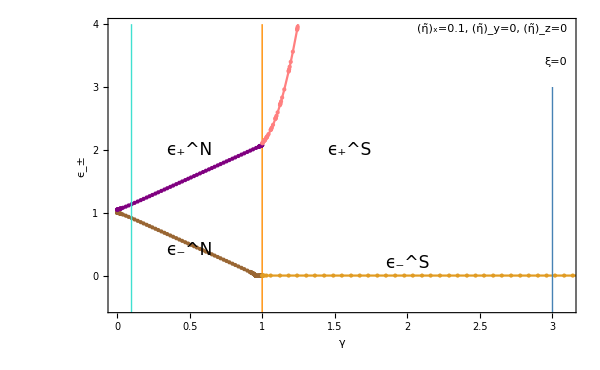

```mathematica
Clear[p]
p[nx_,ny_,nz_,ξ_,ejex_,ejey_,x1_,y1_,x2_,y2_,x3_,y3_,x4_,y4_,g1_,g2_,g3_]:=Show[pt1[nx,ny,nz,ξ,ejex,ejey,x1,y1,x2,y2,x3,y3,x4,y4,g1,g2,g3],pt2[nx,ny,nz,ξ],pt3[nx,ny,nz,ξ],pt4[nx,ny,nz,ξ],Background->White]
p[0.1,0,0,0,cT,cB,0.5,0.4,2,0.2,0.5,2,1.6,2,0.1,1,3]
```